```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10000}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3},11→{0,4},14→{0,3},15→{0,3},18→{-1,3},19→{0,3},20→{0,3},21→{0,7},25→{0,3},26→{0,4},30→{0,3},31→{0,4},35→{0,3},36→{0,2},37→{0,11},38→{0,2},39→{0,4},40→{0,4},41→{-1,3},42→{0,4},43→{0,4},44→{0,4},45→{0,4},46→{-1,3},49→{0,3},56→{0,3},57→{0,3},62→{0,12},63→{0,3},64→{0,3},65→{0,3},66→{0,3},67→{0,3},6996,9923→{-2,3},9924→{0,3},9937→{0,3},9938→{0,3},9939→{0,4},9941→{0,4},9942→{0,8},9943→{0,4},9944→{0,5},9948→{0,3},9949→{-2,4},9950→{0,4},9951→{0,2},9952→{0,3},9965→{0,3},9966→{0,3},9967→{0,4},9969→{0,4},9970→{-3,11},9971→{0,4},9972→{0,5},9974→{0,3},9976→{0,4},9977→{-2,4},9978→{-2,3},9979→{0,3},9990→{0,3},9991→{0,4},9992→{0,4},9993→{0,8},9994→{0,4},9995→{0,5},9998→{0,3},10000→{0,3}}
 |  |  |  |

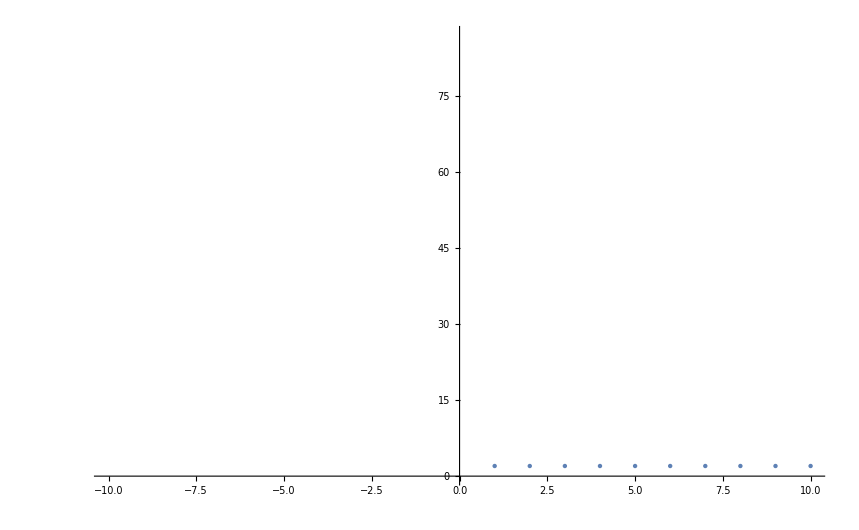

```mathematica
ListPlot[Sort[Map[#[[2,2]]&,Out[602]]], PlotRange->{{-10,10},All}]
```

```mathematica
MpgChain3[ReadGrof[99]]//Reverse//Differences
```

{0,0,0,4,-2,0,0}

```mathematica
MpgChain[ReadGrof[99]]
```

{{1<->2,3},{3<->7,3},{4<->5,3},{6<->9,5},{8<->10,1},{3<->1,1},{6<->4,1},1}

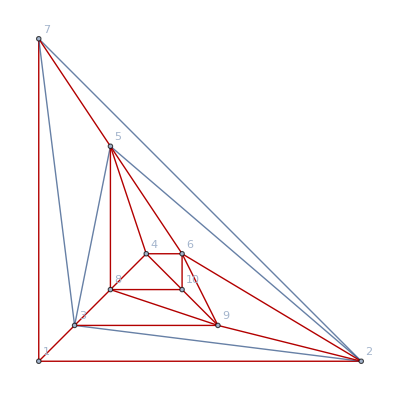

```mathematica
Graph[ReadGrof[99],GraphLayout->"PlanarEmbedding",VertexLabels->"Name",GraphHighlight->CollectMPGEdges[ReadGrof[99]]]
```

```mathematica
MpgChain2[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{Labeled[Graph[g,ImageSize->300,GraphLayout->"PlanarEmbedding",VertexLabelStyle->Directive[Darker[Green],Italic,20],VertexLabels->"Name",GraphHighlightStyle->"Thick",GraphHighlight->CollectMPGEdges[g]],{ChromaticPolynomial[g,4]/24,Map[VertexDegree[g,#]&,VertexList[g]]}]}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain2[contract],{e,Labeled[Graph[g,GraphLayout->"PlanarEmbedding",GraphHighlightStyle->"Thick",VertexLabels->"Name",GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],VertexLabelStyle->Directive[Darker[Green],Italic,20],ImageSize->300, EdgeStyle->{e->{Thick,Blue,Dashed}}],{ChromaticPolynomial[g,4]/24,Map[VertexDegree[g,#]&,VertexList[g]]}]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

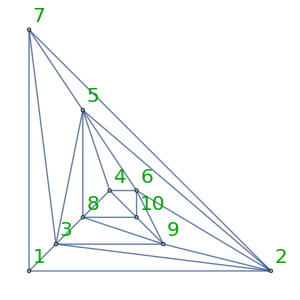
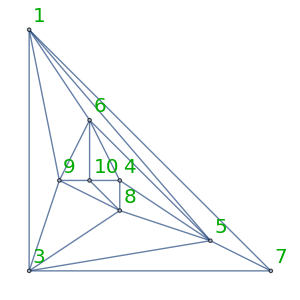
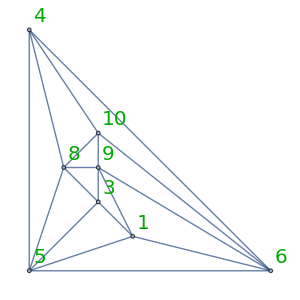
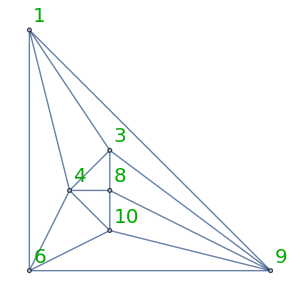
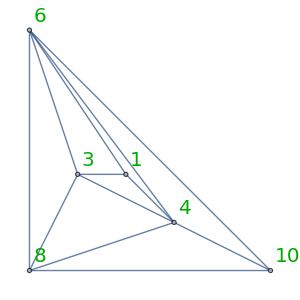
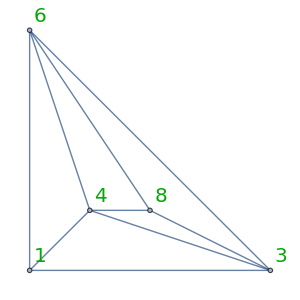
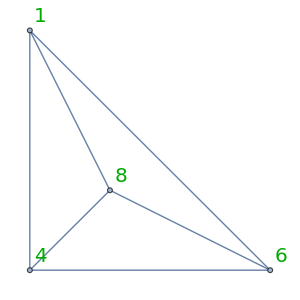
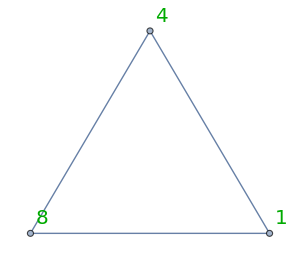
{{1<->2,-Graphics-{3,{3,6,6,4,6,5,5,5,4,4}}},{3<->7,-Graphics-{3,{5,3,6,5,5,5,4,4,5}}},{4<->5,-Graphics-{3,{5,5,5,5,4,4,4,4}}},{6<->9,-Graphics-{5,{4,5,4,4,4,4,5}}},{8<->10,-Graphics-{1,{4,3,3,4,5,5}}},{3<->1,-Graphics-{1,{3,4,4,4,3}}},{6<->4,-Graphics-{1,{3,3,3,3}}},-Graphics-{1,{2,2,2}}}

```mathematica
MpgChain2[ReadGrof[99]]
```

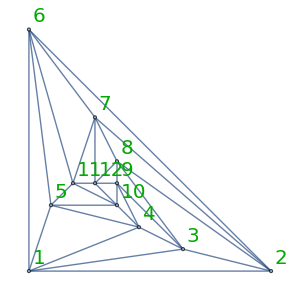
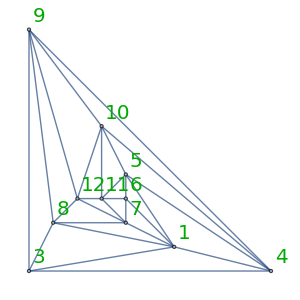
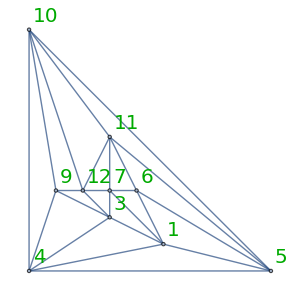
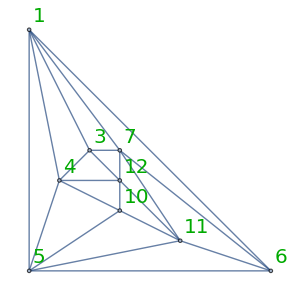
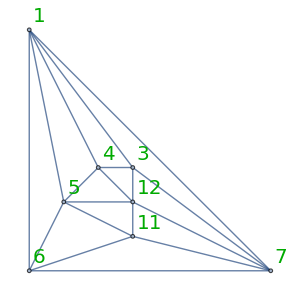
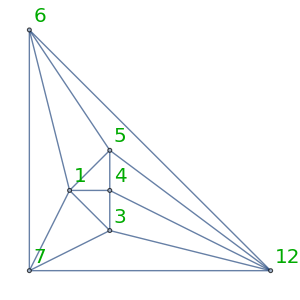
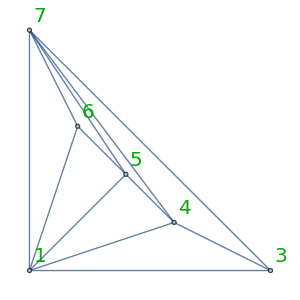
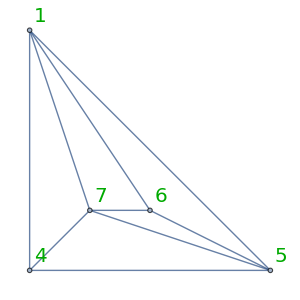
{{1<->2,-Graphics-{10,{5,5,5,5,5,5,5,5,5,5,5,5}}},{3<->8,-Graphics-{8,{4,5,5,4,5,5,5,5,5,5,6}}},{4<->9,-Graphics-{8,{5,5,4,5,4,5,5,5,5,5}}},{5<->10,-Graphics-{2,{5,4,5,4,5,5,5,4,5}}},{6<->11,-Graphics-{3,{4,5,4,5,5,4,4,5}}},{7<->12,-Graphics-{5,{4,5,5,4,4,4,4}}},{3<->1,-Graphics-{1,{5,3,4,4,3,5}}},{5<->4,-Graphics-{1,{3,4,3,4,4}}},{7<->6,-Graphics-{1,{3,3,3,3}}},-Graphics-{1,{2,2,2}}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

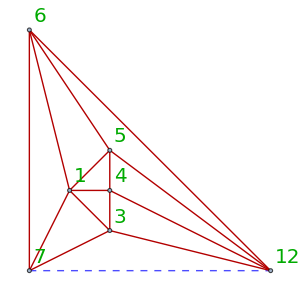
```mathematica
FindFullFormula4[-Graphics-]
```

{v1cx35x46x7,v1cx3x46x57,v1cx36x4x57,v1cx36x47x5,v1cx35x47x6}